```mathematica
gPW92[rs_,v_]:=-2v[[1]](1 + v[[2]]rs)Log[1 + 1/(2v[[1]](v[[3]]rs^(1/2) + v[[4]]rs + v[[5]]rs^(3/2) + v[[6]] rs^2))]
```

```mathematica
unppars={0.031091,0.21370,7.5957,3.5876,1.6382,0.49294};
polpars={0.015545,0.20548,14.1189,6.1977,3.3662,0.62517};
alppars={0.016887,0.11125,10.357,3.6231,0.88026,0.49671};
```

```mathematica
f[z_]:=((1+z)^(4/3) + (1-z)^(4/3) -2)/(2^(4/3)-2);
fdd0=8/(9(2^(4/3)-2));
```

```mathematica
ecPW92[rs_,z_]:=gPW92[rs,unppars](1-f[z]z^4)-gPW92[rs,alppars]f[z] (1- z^4)/fdd0+gPW92[rs,polpars]f[z] z^4
```

```mathematica
g0PW92[rs_]:=0.5(1 + 2(0.193) rs)/(1 + (0.525)rs(1 + (0.193)rs))^2
```

```mathematica
Bpos[rs_]:=(1 + rs^(1/2)(2.15 + 0.435 rs))/(3 + rs^(1/2)(1.57 + 0.409 rs))
```

```mathematica
rstokf=(9Pi/4)^(1/3);
rss3 = Pi rstokf;
kf[rs_]:=rstokf/rs;
ef[rs_]:=kf[rs]^2/2;
ks2[rs_]:=4kf[rs]/Pi
omchi[rs_,z_]:=rs/rss3 - 3 D[ecPW92[rs,y],{y,2}]/(2 ef[rs])/.y->z;
gm0[rs_,z_]:= omchi[rs,z]/ks2[rs];
Amin[rs_,z_]:=kf[rs]^2 gm0[rs,z];
Bmin[rs_]:=Bpos[rs]+2g0PW92[rs]-1;
Cmin[rs_,z_]:=-Pi/(2kf[rs]) (ecPW92[rs,z] + rs D[ecPW92[r,z],r]/.r->rs);
```

```mathematica
gmincms[q_,rs_,n_]:=q^2(Cmin[rs,0] + 1/( 1/(Amin[rs,0]-Cmin[rs,0])^n+(q^2/Bmin[rs])n)^(1/n))
```

```mathematica
Q[q_,rs_]:=q/kf[rs];
```

```mathematica
Manipulate[Plot[{Amin[rs,0]q^2,Cmin[rs,0]q^2 + Bmin[rs],gui[q,a]},{q,0,3}],{rs,1,5},{a,-.5,5}]
```

```mathematica
trs=5;
tdat=Import["/Users/aaronkaplan/Dropbox/phd.nosync/LFF/codes/data_files/CK_Gmin_rs_1.csv","CSV"];
dat=Table[{tdat[[i,1]],tdat[[i,2]]},{i,2,Length[tdat]}];
```

```mathematica
cb = -4/15 ca + 9/4 Amin[trs,0]-3/16 Bmin[trs]+7/4 Cmin[trs,0];
cc = -1/5 ca -3/4 Amin[trs,0]+9/16 Bmin[trs]+3/4Cmin[trs,0];
calp = ca;
cbet = 2/5 ca +9/4 Amin[trs,0]-3/16 Bmin[trs]-9/4 Cmin[trs,0];
cgam=-cc;
```

```mathematica
gui[q_,a_]:=(ca x^4 + cb x^2 + cc +(calp x^4 + cbet x^2 + cgam)(1-x^2)/(2x)Log[Abs[(1+x)/(1-x)]])/.{ca->a,x->q/2}
```

```mathematica
Series[(1-1/c q^4)/(1+b/c q^2+1/c q^4),{q,0,4}]
```

1-(b q^2)/c+((b^2-2 c) q^4)/c^2+O[q]^5

```mathematica
ga=(Bmin[trs]c - b a)/(2c);
gb =(Amin[trs,0]+Cmin[trs,0]-ga b)/2;
gbet =gb-Cmin[trs,0];
galp=-ga;
gui2[q_,aa_,bb_,cc_]:=(ga+ gb q^2 +aa q^4 + (galp+ gbet q^2 +aa q^4)(1-cc q^6)/(1+bb q^2+cc q^6))/.{a->aa,c->cc,b->bb}
```

```mathematica
Remove[ga,gb,gbet,galp]
```

```mathematica
ga=(2c^2 Bmin[trs]+(Cmin[trs,0] -Amin[trs,0])b c+ (b^2 -4c)a)/(4c^2-b^2c);
gb =(Amin[trs,0]+Cmin[trs,0]-a b/c-ga b)/2;
gbet =Amin[trs,0]-gb -ga b;
galp=-ga;
gui2[q_,aa_,bb_,cc_]:=(ga+ gb q^2 +aa q^4 + (galp+ gbet q^2 +aa q^4)(1-cc q^4)/(1+bb q^2+cc q^4))/.{a->aa,c->cc,b->bb}
```

```mathematica
Series[gui2[q,a,b,c],{q,0,2}]
Series[gui2[1/q,a,b,c],{q,0,2}]
```

0.126568 q^2+O[q]^3

0.0508944/q^2+0.0400547-(0.0400547 (-1.88925 b^2+1. b^3+7.557 c-4. b c) q^2)/((b^2-4. c) c)+O[q]^3

```mathematica
Amin[trs,0]
Bmin[trs]
Cmin[trs,0]
```

0.126568

0.0400547

0.0508944

```mathematica
gck[q_,rs_,a_,b_,c_]:=q^2( Amin[rs,0]+a q^2)Exp[-b (q/2)^8]+(Cmin[rs,0]q^2 + Bmin[rs])(1-Exp[-c (q/2)^8])
```

```mathematica
Manipulate[Show[ListPlot[dat],Plot[{gck[q,trs,a,b,c]} ,{q,0,3}],PlotRange->Full],{a,-1,.2},{b,-5,5},{c,-2,5}]
```

ListPlot::lpn: dat is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[dat],,PlotRange→Full].

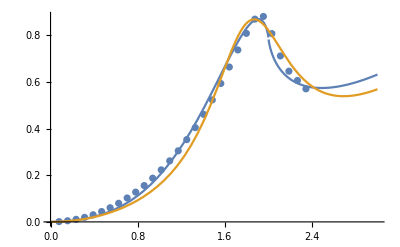

```mathematica
Show[ListPlot[dat],Plot[{gui[q,.853],gui2[q,.009,-.341,.013]} ,{q,0,3}],PlotRange->Full]
```

```mathematica
FindFit[dat,gui2[q,a,b,c],{a,b,c},q]
```

{a→0.00906102,b→-0.341038,c→0.0134566}

```mathematica
alp=Cmin[trs,0]/(1-Bmin[trs])
```

0.0397564

```mathematica
Manipulate[
Show[ListPlot[Table[{dat[[i,1]],dat[[i,2]]/dat[[i,1]]^2/Amin[trs,0]},{i,3,Length[dat]}]],Plot[{1,Bmin[trs]/(Amin[trs,0]q^2)+Cmin[trs,0],(1+a q^2)/(1+ b q^2+c q^4)^(1/2)},{q,0,5},PlotRange->Full]],{a,-5,5},{b,-5,5},{c,.01,5}]
```

```mathematica
iitp[x_,x0_]:=(1-(x/x0)^3(20 - 45 x/x0 + 36 (x/x0)^2-10(x/x0)^3))HeavisideTheta[x0-x]
```

```mathematica
Manipulate[Show[ListPlot[dat],Plot[  Amin[trs,0]q^2iitp[q,a] + (Cmin[trs,0]q^2 + Bmin[trs])(1- iitp[q,a]),{q,0,3},PlotRange->Full]],{a,0.1,100}]
```

ListPlot::lpn: dat is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[dat],].

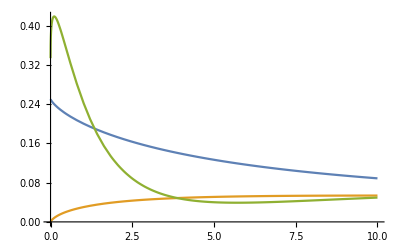

```mathematica
Plot[{Amin[rs,0],Cmin[rs,0],Bmin[rs]},{rs,0,10},PlotRange->Full]
```

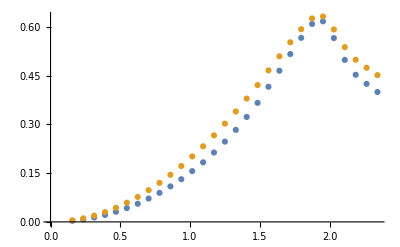

```mathematica
ListPlot[{Table[{dat[[i,1]],.7dat[[i,2]]},{i,2,Length[dat]}],Table[{dat[[i,1]],Log[1+dat[[i,2]]]},{i,2,Length[dat]}]}]
```